Άσκηση 7.6.2-1

Να υπολογιστεί η ρίζα x_2 του παραπάνω συστήματος ακολουθώντας την ίδια διαδικασία.

Λύση

Γράφουμε συνάρτηση που εκτελεί τις παραπάνω πράξεις, ώστε να υπολογίσουμε και τη δεύτερη ρίζα του συστήματος. Εκτελούμε πάλι για n=20 επαναλήψεις.

```mathematica
ClearAll["Global`*"]
solveMC[AA_,bb_,n_]:=Module[
{},
(* υπολογίζουμε τους v και P *)
v=Map[#/Abs[#]&,AA,{2}];
P=Map[Abs[#]&,AA,{2}];
For[i=1,i≤Length[P],i++,AppendTo[P[[i]],1-Total@P[[i]]]];
AppendTo[P,Flatten@{ConstantArray[0,{Length@P}],1}];

(* δημιουργούμε πίνακα με τις τιμές της αθροιστικής συνάρτησης πιθανότητας για κάθε σειρά του πίνακα *)
dim=Dimensions[P][[1]];
Psum=ConstantArray[0,{dim,dim}];
For[ii=1,ii≤dim,ii++,
For[jj=1,jj≤dim,jj++,
Psum[[ii,jj]]=Total[P[[ii,1;;jj]]]
]];

(* υπολογίζουμε τις λύσεις με τη μέθοδο MC *)
sol={};
vars={};
For[m=1,m≤dim-1,m++,
xs={};
For[k=1,k≤n,k++,
i=m;is={i};
While[True,
num=RandomReal[];
i=First@First@Position[Map[num≤#&,Psum[[i]]],True];
AppendTo[is,i];
If[i==dim,Break[]];
];
is=Drop[is,-1];
x=bb[[Last@is]];
While[Length@is>1,
x=bb[[is[[-2]]]]+v[[is[[-2]],is[[-1]]]]x;
is=Drop[is,-1];
];
AppendTo[xs,x];
];
AppendTo[sol,Mean[xs]];
AppendTo[vars,StandardDeviation[xs]];
];

(* επιστρεφουμε τις λύσεις και τις τυπικές αποκλίσεις *)
{sol,vars}
];

AA={{0.1,0.2},{0.1,-0.3}};
bb={0.5,1.1};
answer=solveMC[AA,bb,20];

TableForm[Transpose@{First@answer,Last@answer},TableAlignments->Center,TableHeadings->{{"x_1","x_2"},{"τιμή","σ"}}]
```

| τιμή | σ
x_1 | 0.795 | 0.510392
x_2 | 0.85 | 0.999737

Άσκηση 7.6.2-2

Να συμπληρωθεί το πρόγραμμα prg09_MC_Linear_System ώστε να υπολογίζονται οι διασπορές των εκτιμητών ενός γραμμικού συστήματος n εξισώσεων με n αγνώστους.

Να λυθεί με τη μέθοδο MC ένα σύστημα 10 εξισώσεων με 10 αγνώστους.

Λύση

Δημιουργούμε ένα τυχαίο σύστημα 10×10 και χρησιμοποιούμε τη μέθοδο MC για την επίλυση.

```mathematica
l=10;
A=RandomReal[{-0.1,0.1},{l,l}];
b=RandomReal[{-0.1,0.1},l];

answer=solveMC[A,b,1000];
TableForm[Transpose@{First@answer,Last@answer},TableAlignments->Center,TableHeadings->{Table[StringForm["x_(``)",i],{i,1,l}],{"τιμή","σ"}}]
```

| τιμή | σ
x_(RowBox[{) | 0.0045813 | 0.041539
x_(RowBox[{) | -0.0167889 | 0.0474325
x_(RowBox[{) | 0.036988 | 0.0434171
x_(RowBox[{) | -0.0571717 | 0.0400639
x_(RowBox[{) | -0.0155152 | 0.0440601
x_(RowBox[{) | -0.00978823 | 0.0404649
x_(RowBox[{) | 0.0488857 | 0.0417629
x_(RowBox[{) | 0.0579459 | 0.040765
x_(RowBox[{) | 0.0643717 | 0.0426963
x_(RowBox[{) | 0.0782367 | 0.0405415

Από τις δύο παραπάνω ασκήσεις βλέπουμε ότι η μέθοδος ακόμα και για πολύ μικρά δείγματα (n=20 στην 1^η περίπτωση) δίνει αρκετά ακριβή αποτελέσματα, ενώ για μεγάλα δείγματα η ακρίβεια βελτιώνεται χωρίς να αυξάνεται ιδιαίτερα ο χρόνος εκτέλεσης.

Επομένως η μέθοδος μπορεί να φανεί χρήσιμη στην επαναλβανόμενη επίλυση συστημάτων με μεγάλο αριθμό εξισώσεων, για τα οποία δεν θέλουμε τεράστια ακρίβεια αλλά δεν θέλουμε και να καταναλώνει η επίλυση πολύ χρόνο.

Άσκηση 7.7.1-1

Να προσδιοριστεί ο αριθμός των πυρήνων ^134 I_53 ως συνάρτηση του χρόνου, αν είναι γνωστό ότι N_0=10^3 και τα χρονικά διαστήματα των μετρήσεων είναι

κάθε 30sec

κάθε 1min

κάθε 2min

Να γίνει σύγκριση των αποτελεσμάτων με τις τιμές που παίρνουμε από τη σχέση (21).

Λύση

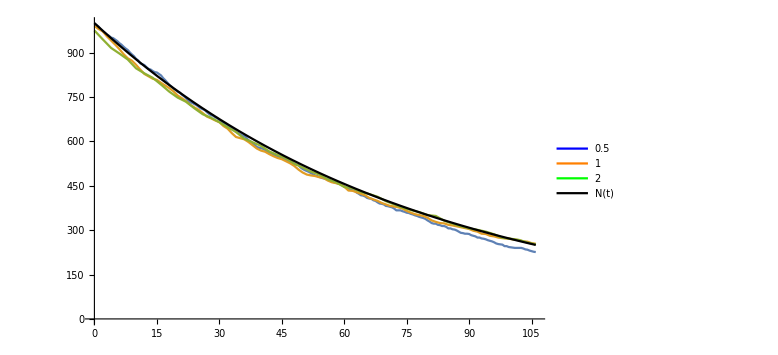

```mathematica
ClearAll["Global`*"]
(* ορίζουμε την αναλυτική συνάρτηση *)
NN[t_]:=N0 ⅇ^(-λ t)

(* ορίζουμε τις σταθερές *)
N0=10^3;
Thalf=53(*min*);
λ=Log[2]/Thalf//N;
tmax=2Thalf;

(* υπολογίζουμε τις διασπάσεις σε κάθε περίπτωση *)
Nall={};
Do[
Ns={};Ncurrent=N0;
(* βρόχος για την αλλαγή του χρονικού βήματος *)
For[t=0,t≤tmax,t+=dt,
(* βρόχος για τον χρόνο *)
n=Ncurrent;
For[i=1,i≤n,i++,
(* βρόχος για τη διάσπαση κάθε πυρήνα *)
If[RandomReal[]≤λ dt,Ncurrent-=1]
];
AppendTo[Ns,{t,Ncurrent}]
];
AppendTo[Nall,Ns];
,{dt,{0.5,1,2}}]

ListPlot[Nall,ImageSize->Large,Epilog->First@Plot[NN[t],{t,0,tmax},PlotStyle->Black],Joined->True,PlotLegends->LineLegend[{Blue,Orange,Green,Black},{"0.5","1","2","N(t)"}]]
```

Παρατηρούμε ότι η μέθοδος είναι αποτελεσματική, δείνει το ίδιο αποτέλεσμα με την αναλυτική συνάρτηση στην περίπτωση αυτή, η οποία όμως δεν μπορεί να χρησιμοποιηθεί πάντοτε. Επομένως έχουμε ένα χρήσιμο εργαλείο για τις περιπώσης που η έκφραση N(t)=N_0 ⅇ^(-λ t) δεν είναι ακριβής.